# Epidemic Programming Language Adoption

## Analysis of programming language adoption using the Richards cumulative growth function applied in an epidemic context

## Defining the model and importing data

```mathematica
richards[k_,r_,tm_,a_,t_]:=k/(1+Exp[-r(t-tm)])^(1/a);
```

```mathematica
fitModelToDataset[data_,model_,initialK_]:=NonlinearModelFit[data,model[k,r,tm,a,t],{{k,initialK},r,tm,a},t,MaxIterations->100000];
```

```mathematica
language="CSharp";
```

```mathematica
percentage=90;
```

```mathematica
runTests=1;(*set this to 1 to run the statistical tests, set to 0 to skip them (saves time when tuning the parameters)*)
```

```mathematica
export=1;(*set export to 1 if you want to export all results when evaluating the entire notebook*)
```

```mathematica
initialk=300000;
```

```mathematica
direction=1;(* 1 if you want to remove elements from the tail of the dataset, -1 if you want to remove elements from the head of the dataset *)
```

```mathematica
dataFilePath="C:\\Users\\emano\\Dropbox\\UFPE\\Doutorado\\Dados\\github\\ghtorrent\\mathematica\\programadores\\semana";
```

```mathematica
dataFileName=StringJoin["dados_",language,"_semana.dat"];
```

```mathematica
dataFull=Import[FileNameJoin[{dataFilePath,dataFileName}]];
```

```mathematica
exportPath=StringJoin[dataFilePath,"\\processado_tail"];
```

```mathematica
mean[data_]:=Mean[data[[All,2]]];
```

```mathematica
ssRes[data_,model_]:=Sum[(data[[t,2]]-model[t])^2,{t,1,Length[data]}];
```

```mathematica
ssTot[data_]:=Sum[(data[[t,2]]-Mean[data[[All,2]]])^2,{t,1,Length[data]}];
```

```mathematica
rsquared[data_,model_]:=1-ssRes[data,model]/ssTot[data];
```

## Fitting the model to the data

```mathematica
fittedFull=fitModelToDataset[dataFull,richards,initialk];
```

```mathematica
fittedFull["BestFitParameters"]
```

{k→1.99248×10^6,r→0.0050111,tm→-1998.69,a→3.04288×10^-6}

```mathematica
dataPart=Take[dataFull,Round[Length[dataFull]*(percentage/100)]];
```

```mathematica
fittedPart=fitModelToDataset[dataPart,richards,initialk];
```

```mathematica
fittedPart["BestFitParameters"]
```

{k→1.99248×10^6,r→0.0050111,tm→-1998.69,a→3.04288×10^-6}

## Plotting the results of the fit

```mathematica
dataplotFull=ListPlot[dataFull[[1;;-1;;6]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"▲"}];
```

```mathematica
dataplotPart=ListPlot[dataPart[[1;;-1;;6]],PlotStyle->{Black,PointSize[0.01]},PlotMarkers->{"●"}];
```

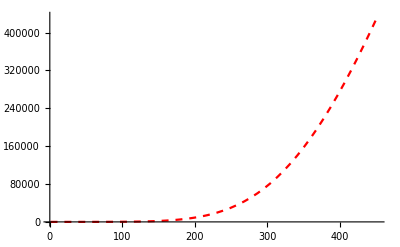

```mathematica
fitplotFull=Plot[fittedFull[t],{t,1,Length[dataFull]*1.1},PlotStyle->{Red,Dashed},PlotRange->All]
```

```mathematica
fitplotPart=Plot[fittedPart[t],{t,1,Length[dataFull]*1.11},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Fit Plot",PlotRange->All];
```

```mathematica
graphFit=If[percentage==100,Show[fitplotPart,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All],Show[fitplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]]
```

-Graphics-

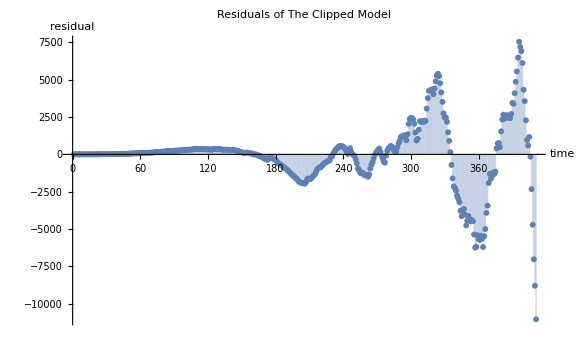

```mathematica
graphResidual=ListPlot[fittedPart["FitResiduals"],AxesLabel->{"time","residual"},Filling->Axis,ImageSize->Large,PlotLabel->"Residuals of The Clipped Model",PlotRange->All]
```

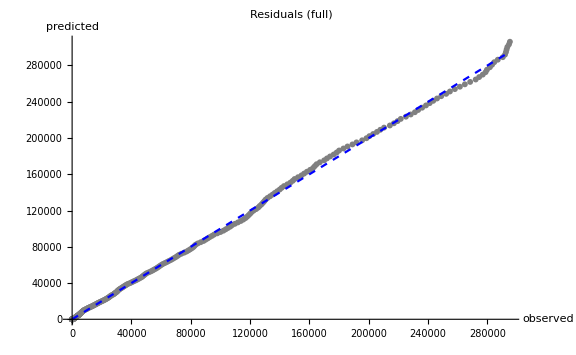

```mathematica
graphResidual2=Show[ListPlot[Transpose[{dataFull[[All,2]],fittedFull["PredictedResponse"]}],PlotStyle->Gray],Plot[x,{x,0,Max[dataFull[[All,2]]]},PlotStyle->{Dashed,Blue}],ImageSize->Large,AxesLabel->{"observed","predicted"},PlotLabel->"Residuals (full)"]
```

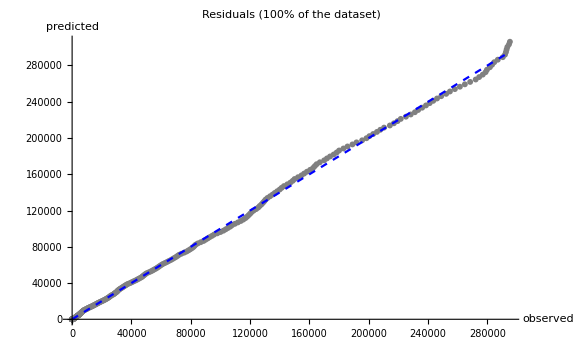

```mathematica
graphResidual3=Show[ListPlot[Transpose[{dataPart[[All,2]],fittedPart["PredictedResponse"]}],PlotStyle->Gray],Plot[x,{x,0,Max[dataPart[[All,2]]]},PlotStyle->{Dashed,Blue}],ImageSize->Large,AxesLabel->{"observed","predicted"},PlotLabel->"Residuals ("<>ToString[percentage]<>"% of the dataset)"]
```

```mathematica
Button["Export residual plots",Export[FileNameJoin[{exportPath,StringJoin["residualPlot_",language,"_",ToString[percentage],".eps"]}],graphResidual,"EPS"];Export[FileNameJoin[{exportPath,StringJoin["residualPlotLineFull_",language,"_",ToString[percentage],".eps"]}],graphResidual2,"EPS"];Export[FileNameJoin[{exportPath,StringJoin["residualPlotLineClipped_",language,"_",ToString[percentage],".eps"]}],graphResidual3,"EPS"]]
```

Export residual plots

## Hypothesis tests for the model from the clipped dataset

```mathematica
hypothesisTestTable=Table[{t,fittedPart[t]},{t,1,Length[dataFull]}];
```

```mathematica
(*windowSize=100;*)
```

```mathematica
(*hypothesisTest=Table[GoodmanKruskalGammaTest[Take[dataFull[[All,2]],{index,windowSize+index-1}],Take[hypothesisTestTable[[All,2]],{index,windowSize+index-1}],"PValue"],{index,1,Length[dataFull]-windowSize+1}]*)
```

```mathematica
hypothesisTest=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTable,"HypothesisTestData"]]
```

$Aborted[]

```mathematica
Button["Export hypothesis test data",Export[FileNameJoin[{exportPath,StringJoin[language,"_",ToString[percentage],"_hypothesisTestClipped.txt"]}],Table[{prop,hypothesisTest[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}]]]
```

Export hypothesis test data

## Trying to improve the model with residual analysis

```mathematica
dampedCosine[b_,lambda_,omega_,fi_,shift_,t_]:=b*Exp[-lambda*t]*Cos[omega*t+fi]+shift;
```

```mathematica
gaussianSine[amp_,freq_,qual_,shift_,t_]:=amp*Exp[-((t-shift)^2) ((4 π^2 freq^2)/qual^2)] Sin[2 π freq (t-shift)];
```

## Iteration 1

### Trying to fit the damped cosine to the raw residuals (iteration 1)

```mathematica
fittedResidual1=NonlinearModelFit[fittedPart["FitResiduals"],dampedCosine[b,lambda,omega,fi,shift,t],{{lambda,0.008678155310838227},{omega,0.024150174601298917},{fi,-4.4632769483010675},{b,2480.8039600567104},{shift,249.3166993138453}},t,MaxIterations->100000]
```

FittedModel[-7.99487-10.2268 ⅇ^(0.00116314 t) Cos[23.9125-0.0122548 t]]

```mathematica
fittedResidual1["BestFitParameters"]
```

{lambda→-0.00116314,omega→0.0122548,fi→-23.9125,b→-10.2268,shift→-7.99487}

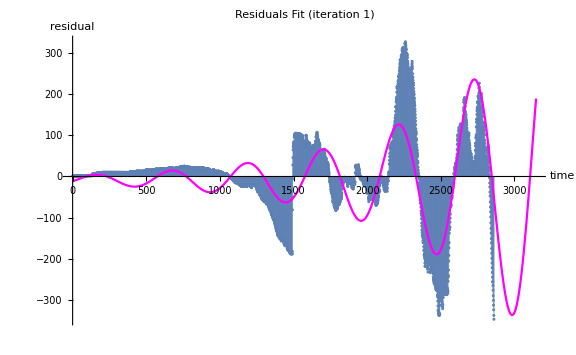

```mathematica
graphFittedResidual1=Show[ListPlot[fittedPart["FitResiduals"],Filling->Axis,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 1)"],Plot[fittedResidual1[t],{t,0,Length[dataPart]*1.1},PlotStyle->Magenta,PlotRange->All],ImageSize->Large,PlotRange-> All]
```

```mathematica
(*Manipulate[Show[ListPlot[fittedPart["FitResiduals"]],Plot[dampedCosine[b,lambda,omega,fi,shift,t],{t,0,400},PlotRange->All],ImageSize-> Large,PlotRange-> All],{{lambda,-0.07},-1,2,0.001},{{omega,0.3},0.001,10,0.001},{{fi,-0.03},-20,20,0.01},{{b,33},-20,50,0.1},{shift,-50,50}]*)
```

```mathematica
correctedDampedModel1[t_]:=fittedResidual1[t]+fittedPart[t];
```

```mathematica
graphModelWithResidual1=Show[Plot[correctedDampedModel1[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 1)"],dataplotFull,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newResidual1=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedDampedModel1[t],{t,1,Length[dataPart]}]}];
```

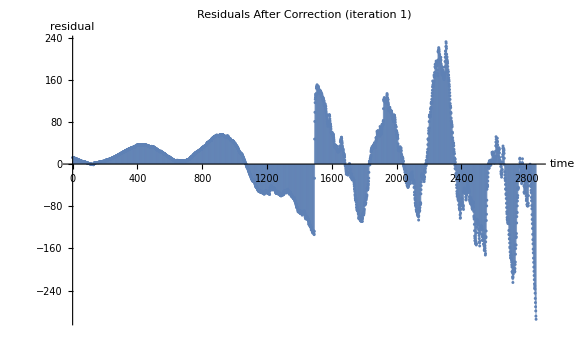

```mathematica
graphNewResidual1=ListPlot[newResidual1,ImageSize->Large,Filling->Axis,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 1)"]
```

### Trying to fit the sine-modulated gaussian to the residuals (iteration 1)

```mathematica
fittedGaussianResidual1=NonlinearModelFit[fittedPart["FitResiduals"],gaussianSine[amp,freq,qual,shift,t],{{amp,300},{freq,0.001},{qual,1},{shift,2500}},t,MaxIterations->100000];
```

```mathematica
fittedGaussianResidual1["BestFitParameters"]
```

{amp→276.574,freq→0.00215834,qual→6.85504,shift→2590.5}

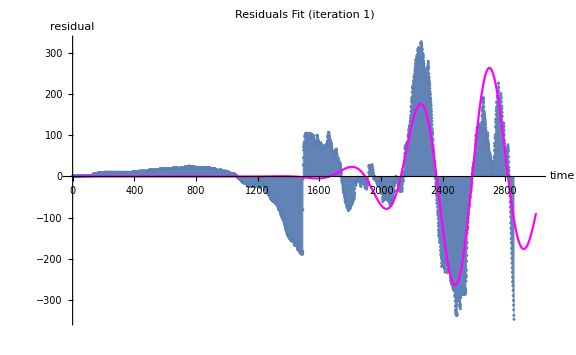

```mathematica
graphFittedGaussianResidual1=Show[ListPlot[fittedPart["FitResiduals"],Filling-> Axis,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 1)"],Plot[fittedGaussianResidual1[t],{t,0,Length[dataPart]*1.05},PlotStyle->Magenta,PlotRange->All],ImageSize->Large,PlotRange->All]
```

```mathematica
correctedGaussianModel1[t_]:=fittedGaussianResidual1[t]+fittedPart[t];
```

```mathematica
graphGaussianModelWithResidual1=Show[Plot[correctedGaussianModel1[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 1)"],dataplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newGaussianResidual1=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedGaussianModel1[t],{t,1,Length[dataPart]}]}];
```

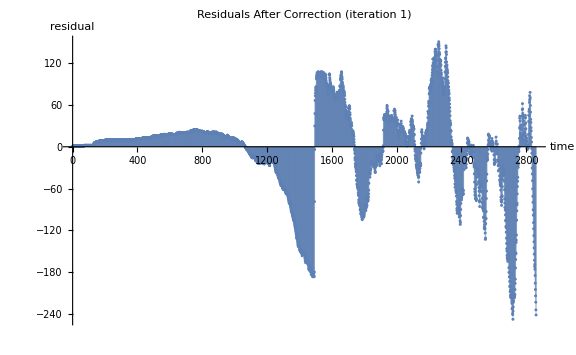

```mathematica
graphNewGaussianResidual1=ListPlot[newGaussianResidual1,ImageSize->Large,PlotRange->All,Filling-> Axis,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 1)"]
```

## Iteration 2

### Trying to fit the damped cosine to the raw residuals (iteration 2)

```mathematica
fittedResidual2=NonlinearModelFit[newResidual1,dampedCosine[b,lambda,omega,fi,shift,t],{{lambda,lambda/.fittedResidual1["BestFitParameters"]},{omega,omega/.fittedResidual1["BestFitParameters"]},{fi,fi/.fittedResidual1["BestFitParameters"]},{b,b/.fittedResidual1["BestFitParameters"]},{shift,shift/.fittedResidual1["BestFitParameters"]}},t,MaxIterations->100000]
```

FittedModel[3.04303+7.56762 ⅇ^(0.000855738 t) Cos[20.1012-0.0087457 t]]

```mathematica
fittedResidual2["BestFitParameters"]
```

{lambda→-0.000855738,omega→0.0087457,fi→-20.1012,b→7.56762,shift→3.04303}

```mathematica
(*Manipulate[Show[ListPlot[newResidual1],Plot[dampedCosine[b,lambda,omega,fi,shift,t],{t,0,3000},PlotRange->All],ImageSize-> Large,PlotRange-> All],{{lambda,0.008678155310838227},-1,2,0.001},{{omega,0.024150174601298917},0.001,10,0.001},{{fi,-4.4632769483010675},-20,20,0.01},{{b,2480.8039600567104},-20,3000,0.1},{{shift,0},-50,50}]*)
```

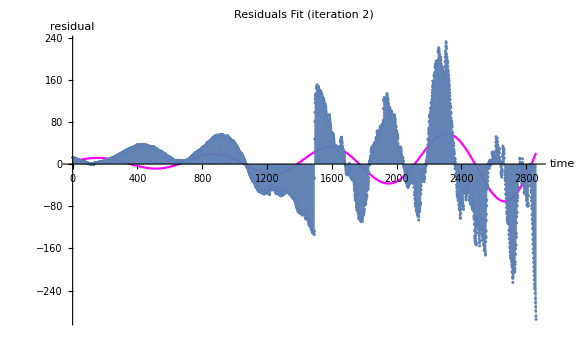

```mathematica
graphFittedResidual2=Show[Plot[fittedResidual2[t],{t,0,Length[dataPart]*1},PlotStyle->Magenta,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 2)"],ListPlot[newResidual1,Filling-> Axis],ImageSize->Large,PlotRange-> All]
```

```mathematica
correctedDampedModel2[t_]:=fittedResidual2[t]+correctedDampedModel1[t];
```

```mathematica
graphModelWithResidual2=Show[Plot[correctedDampedModel2[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 2)"],fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newResidual2=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedDampedModel2[t],{t,1,Length[dataPart]}]}];
```

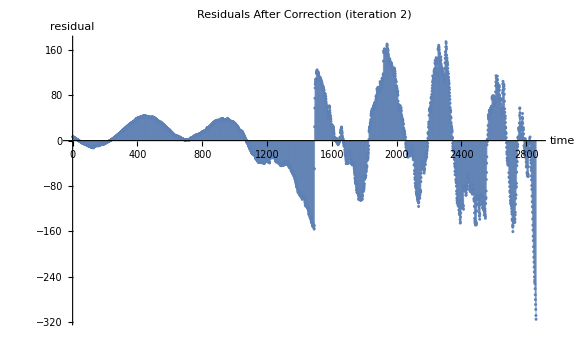

```mathematica
graphNewResidual2=ListPlot[newResidual2,ImageSize->Large,Filling->Axis,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 2)"]
```

### Trying to fit the sine-modulated gaussian to the raw residuals (iteration 2)

```mathematica
fittedGaussianResidual2=NonlinearModelFit[newGaussianResidual1,gaussianSine[amp,freq,qual,shift,t],{{amp,300},{freq,0.04},{qual,1},{shift,1500}},t,MaxIterations->100000];
```

```mathematica
fittedGaussianResidual2["BestFitParameters"]
```

{amp→61449.2,freq→7.89889×10^-6,qual→0.00564454,shift→1502.76}

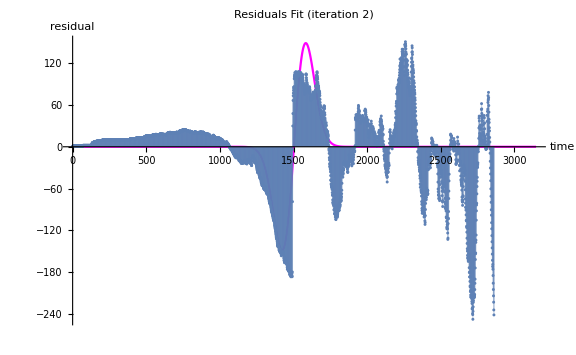

```mathematica
graphFittedGaussianResidual2=Show[Plot[fittedGaussianResidual2[t],{t,0,Length[dataPart]*1.1},PlotStyle->Magenta,PlotRange->All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 2)"],ListPlot[newGaussianResidual1,Filling->Axis],ImageSize->Large,PlotRange-> All]
```

```mathematica
correctedGaussianModel2[t_]:=fittedGaussianResidual2[t]+correctedGaussianModel1[t];
```

```mathematica
graphGaussianModelWithResidual2=Show[Plot[correctedGaussianModel2[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 2)"],fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newGaussianResidual2=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedGaussianModel2[t],{t,1,Length[dataPart]}]}];
```

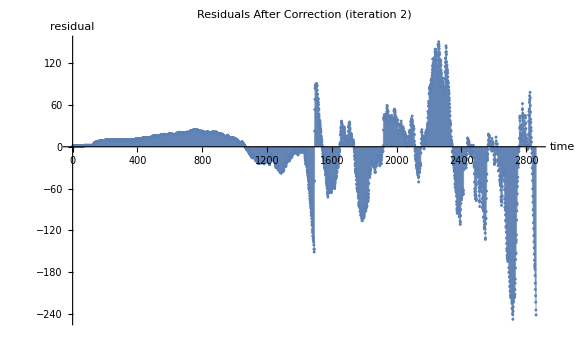

```mathematica
graphNewGaussianResidual2=ListPlot[newGaussianResidual2,ImageSize->Large,Filling->Axis,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 2)"]
```

## Iteration 3

### Trying to fit the damped cosine to the raw residuals (iteration 3)

```mathematica
fittedResidual3=NonlinearModelFit[newResidual2,dampedCosine[b,lambda,omega,fi,shift,t],{{lambda,lambda/.fittedResidual2["BestFitParameters"]},{omega,2*omega/.fittedResidual2["BestFitParameters"]},{fi,fi/.fittedResidual2["BestFitParameters"]},{b,200},{shift,shift/.fittedResidual2["BestFitParameters"]}},t,MaxIterations->100000];
```

```mathematica
fittedResidual3["BestFitParameters"]
```

{lambda→-0.000691426,omega→0.0179802,fi→-22.1892,b→17.2905,shift→2.12698}

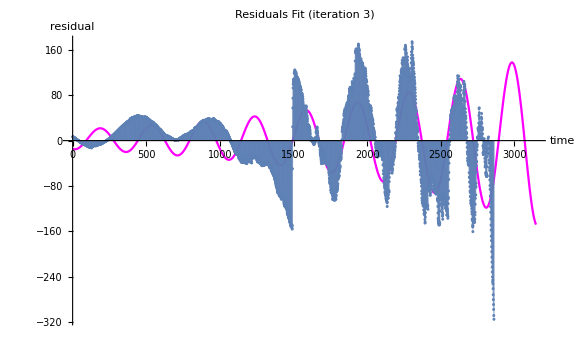

```mathematica
graphFittedResidual3=Show[Plot[fittedResidual3[t],{t,0,Length[dataPart]*1.1},PlotStyle->Magenta,PlotRange-> All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 3)"],ListPlot[newResidual2,Filling->Axis],ImageSize->Large,PlotRange-> All]
```

```mathematica
correctedDampedModel3[t_]:=fittedResidual3[t]+correctedDampedModel2[t];
```

```mathematica
graphModelWithResidual3=Show[Plot[correctedDampedModel3[t],{t,0,Length[dataFull]*1.13},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 3)"],dataplotPart,fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newResidual3=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedDampedModel3[t],{t,1,Length[dataPart]}]}];
```

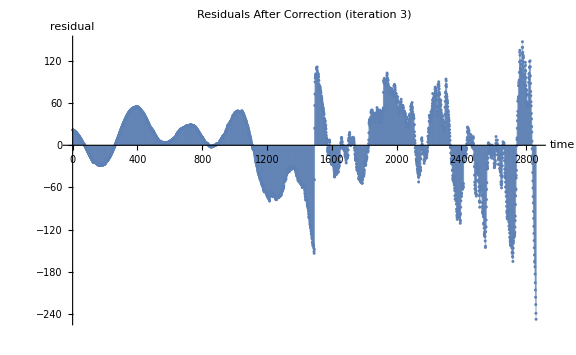

```mathematica
graphNewResidual2=ListPlot[newResidual3,ImageSize->Large,Filling->Axis,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 3)"]
```

### Trying to fit the sine-modulated gaussian to the raw residuals (iteration 3)

```mathematica
fittedGaussianResidual3=NonlinearModelFit[newGaussianResidual2,gaussianSine[amp,freq,qual,shift,t],{{amp,150},{freq,0.001},{qual,5},{shift,2300}},t,MaxIterations->100000];
```

```mathematica
fittedGaussianResidual3["BestFitParameters"]
```

{amp→-78.2677,freq→0.00100468,qual→4.08486,shift→2423.29}

```mathematica
(*Manipulate[Show[ListPlot[newGaussianResidual2,Filling->Axis],Plot[gaussianSine[amp,freq,qual,shift,t],{t,0,400},PlotRange->All],ImageSize-> Large,PlotRange-> All],{{amp,10000},-10000,10000,10},{{freq,0.01},-10,10,0.001},{{qual,10},-50,50,1},{{shift,320},0,500,1}]*)
```

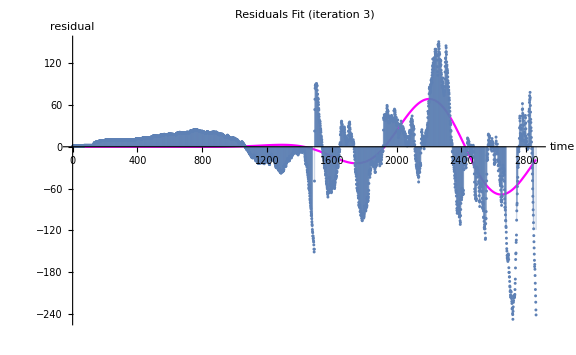

```mathematica
graphFittedGaussianResidual3=Show[Plot[fittedGaussianResidual3[t],{t,0,Length[dataPart]*1},PlotStyle->Magenta,PlotRange->All,AxesLabel->{"time","residual"},PlotLabel->"Residuals Fit (iteration 3)"],ListPlot[newGaussianResidual2,Filling->Axis],ImageSize->Large,PlotRange-> All]
```

```mathematica
correctedGaussianModel3[t_]:=fittedGaussianResidual3[t]+correctedGaussianModel2[t];
```

```mathematica
graphGaussianModelWithResidual3=Show[Plot[correctedGaussianModel3[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After Residual Correction (iteration 3)"],fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange-> All]
```

-Graphics-

```mathematica
newGaussianResidual3=Transpose[{Table[t,{t,1,Length[dataPart]}],Table[dataPart[[t,2]]-correctedGaussianModel3[t],{t,1,Length[dataPart]}]}];
```

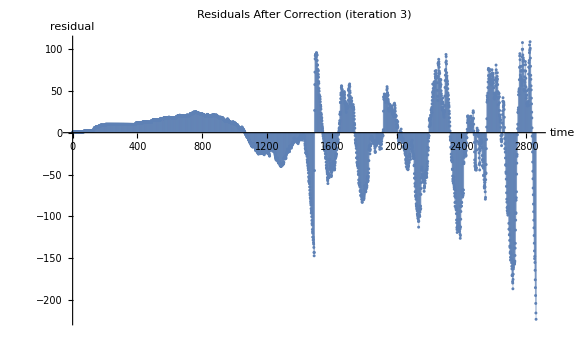

```mathematica
graphNewGaussianResidual3=ListPlot[newGaussianResidual3,ImageSize->Large,PlotRange->All,Filling->Axis,AxesLabel->{"time","residual"},PlotLabel->"Residuals After Correction (iteration 3)"]
```

### Final correction results

```mathematica
graphFinalCorrectedDamped=Show[Plot[correctedDampedModel3[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After 3 Iterations of Residual Correction"],fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]
```

-Graphics-

```mathematica
graphFinalCorrectedGaussian=Show[Plot[correctedGaussianModel3[t],{t,0,Length[dataFull]*1.15},PlotStyle->Blue,AxesLabel->{"time","cumulative infected"},PlotLabel->"Model After 3 Iterations of Residual Correction"],fitplotFull,dataplotFull,dataplotPart,ImageSize->Large,PlotRange->All]
```

-Graphics-

## Statistics

In this section I will run the statistical tests for every model, starting from the raw one and moving to the ones corrected by the residuals. Also, the coefficient of determination is calculated.

## Hypothesis tests for the corrected models

## Damped cosine

```mathematica
hypothesisTestTableDampedCosine1=Table[{t,correctedDampedModel1[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestDampedCosine1=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableDampedCosine1,"HypothesisTestData"],Null]
```

HypothesisTestData[…]

```mathematica
hypothesisTestTableDampedCosine2=Table[{t,correctedDampedModel2[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestDampedCosine2=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableDampedCosine2,"HypothesisTestData"],Null]
```

$Aborted[]

```mathematica
hypothesisTestTableDampedCosine3=Table[{t,correctedDampedModel3[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestDampedCosine3=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableDampedCosine3,"HypothesisTestData"],Null]
```

## Sine-modulated gaussian

```mathematica
hypothesisTestTableGaussian1=Table[{t,correctedGaussianModel1[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestGaussian1=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableGaussian1,"HypothesisTestData"],Null]
```

```mathematica
hypothesisTestTableGaussian2=Table[{t,correctedGaussianModel2[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestGaussian2=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableGaussian2,"HypothesisTestData"],Null]
```

```mathematica
hypothesisTestTableGaussian3=Table[{t,correctedGaussianModel3[t]},{t,1,Length[dataFull]}];
```

```mathematica
hypothesisTestGaussian3=If[runTests==1,DistributionFitTest[dataFull,hypothesisTestTableGaussian3,"HypothesisTestData"],Null]
```

```mathematica
(*windowSize=300;*)
```

```mathematica
(*hypothesisTestWindow=Table[1-KolmogorovSmirnovTest[Take[dataFull[[All,2]],{index,windowSize+index-1}],Take[hypothesisChiSquareGaussian[[All,2]],{index,windowSize+index-1}],"PValue"],{index,1,Length[dataFull]-windowSize+1}];*)
```

```mathematica
(*ListPlot[hypothesisTestWindow,Filling->Axis,ImageSize->Large]*)
```

## Comparing the coefficient of determination between the fitted models and the corrected models

```mathematica
rsquared1=rsquared[dataFull,fittedFull]
```

0.999406

```mathematica
rsquared2=rsquared[dataPart,fittedPart]
```

0.999406

```mathematica
rsquared3=rsquared[dataFull,fittedPart]
```

0.999406

```mathematica
rsquared4=rsquared[dataFull,correctedGaussianModel1]
```

0.999406

```mathematica
rsquared5=rsquared[dataFull,correctedGaussianModel2]
```

0.999406

```mathematica
rsquared6=rsquared[dataFull,correctedGaussianModel3]
```

0.999508

```mathematica
rsquared7=rsquared[dataFull,correctedDampedModel1]
```

0.999711

```mathematica
rsquared8=rsquared[dataFull,correctedDampedModel2]
```

0.999733

```mathematica
rsquared9=rsquared[dataFull,correctedDampedModel3]
```

0.999737

```mathematica
exportFitParams[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fitParams.txt"]}],fittedPart["BestFitParameters"],"Text"];
```

```mathematica
exportFitPlot[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fitPlot.eps"]}],graphFit,"EPS"];
```

```mathematica
exportResidualsOriginal[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","residualPlot.eps"]}],graphResidual,"EPS"];
```

```mathematica
exportResidualsLineFull[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","residualPlotLineFull.eps"]}],graphResidual2,"EPS"];
```

```mathematica
exportResidualsLineClipped[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","residualPlotLineClipped.eps"]}],graphResidual3,"EPS"];
```

```mathematica
exportFitParamsResidualGaussianCorrections[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fitParamsGaussianResidualCorrection.txt"]}],ToString[fittedGaussianResidual1["BestFitParameters"]]<>"\n"<>ToString[fittedGaussianResidual2["BestFitParameters"]]<>"\n"<>ToString[fittedGaussianResidual3["BestFitParameters"]],"Text"];
```

```mathematica
exportFitParamsResidualDampedCorrections[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fitParamsDampedResidualCorrection.txt"]}],ToString[fittedResidual1["BestFitParameters"]]<>"\n"<>ToString[fittedResidual2["BestFitParameters"]]<>"\n"<>ToString[fittedResidual3["BestFitParameters"]],"Text"];
```

```mathematica
exportFinalCorrectionDamped[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","finalCorrectedDamped.eps"]}],graphFinalCorrectedDamped,"EPS"];
```

```mathematica
exportFinalCorrectionGaussian[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","finalCorrectedGaussian.eps"]}],graphFinalCorrectedGaussian,"EPS"];
```

```mathematica
b1 =Button["Export all results part 1",exportFitPlot[];exportResidualsOriginal[];exportResidualsLineFull[];exportResidualsLineClipped[];exportFitParamsResidualGaussianCorrections[];exportFitParamsResidualDampedCorrections[];exportFinalCorrectionGaussian[]];
```

```mathematica
exportFittedGaussianResidualAnalysis1[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianResidual1.eps"]}],graphFittedGaussianResidual1,"EPS"];
```

```mathematica
exportFittedGaussianResidualAnalysis2[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianResidual2.eps"]}],graphFittedGaussianResidual2,"EPS"];
```

```mathematica
exportFittedGaussianResidualAnalysis3[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianResidual3.eps"]}],graphFittedGaussianResidual3,"EPS"];
```

```mathematica
exportFittedGaussianResidualResult1[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianPartialResult1.eps"]}],graphGaussianModelWithResidual1,"EPS"];
```

```mathematica
exportFittedGaussianResidualResult2[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianPartialResult2.eps"]}],graphGaussianModelWithResidual2,"EPS"];
```

```mathematica
exportFittedGaussianResidualResult3[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedGaussianPartialResult3.eps"]}],graphGaussianModelWithResidual3,"EPS"];
```

```mathematica
exportFittedDampedResidualAnalysis1[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedResidual1.eps"]}],graphFittedResidual1,"EPS"];
```

```mathematica
exportFittedDampedResidualAnalysis2[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedResidual2.eps"]}],graphFittedResidual2,"EPS"];
```

```mathematica
exportFittedDampedResidualAnalysis3[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedResidual3.eps"]}],graphFittedResidual3,"EPS"];
```

```mathematica
exportFittedDampedResidualResult1[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedPartialResult1.eps"]}],graphModelWithResidual1,"EPS"];
```

```mathematica
exportFittedDampedResidualResult2[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedPartialResult2.eps"]}],graphModelWithResidual2,"EPS"];
```

```mathematica
exportFittedDampedResidualResult3[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","fittedDampedPartialResult3.eps"]}],graphModelWithResidual3,"EPS"];
```

```mathematica
b2=Button["Export all results part 2",exportFinalCorrectionDamped[];exportFittedDampedResidualAnalysis1[];exportFittedDampedResidualAnalysis2[];exportFittedDampedResidualAnalysis3[];exportFittedGaussianResidualAnalysis1[];exportFittedGaussianResidualAnalysis2[];exportFittedGaussianResidualAnalysis3[]];
```

```mathematica
exportStatistics1:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","hypothesisTest.txt"]}],Join[Table[{prop,hypothesisTestDampedCosine1[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}],Table[{prop,hypothesisTestDampedCosine2[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}],Table[{prop,hypothesisTestDampedCosine3[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}],Table[{prop,hypothesisTestGaussian1[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}],Table[{prop,hypothesisTestGaussian2[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}],Table[{prop,hypothesisTestGaussian3[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}]]];
```

```mathematica
exportStatistics2:=Export[FileNameJoin[{exportPath,StringJoin[language,"_",ToString[percentage],"_hypothesisTestClipped.txt"]}],Table[{prop,hypothesisTest[prop]},{prop,{"ShortTestConclusion","PValue","TestStatistic"}}]];
```

```mathematica
exportR2[]:=Export[FileNameJoin[{exportPath,StringJoin[language,ToString[percentage],"_","rsquared.txt"]}],"fittedFull-dataFull->"<>ToString[rsquared1]<>"\n"<>"fittedPart-dataPart->"<>ToString[rsquared2]<>"\n"<>"fittedPart-dataFull->"<>ToString[rsquared3]<>"\n"<>"gaussianCorrected1-dataFull->"<>ToString[rsquared4]<>"\n"<>"gaussianCorrected2-dataFull->"<>ToString[rsquared5]<>"\n"<>"gaussianCorrected3-dataFull->"<>ToString[rsquared6]<>"\n"<>"correctedDamped1-dataFull->"<>ToString[rsquared7]<>"\n"<>"correctedDamped2-dataFull->"<>ToString[rsquared8]<>"\n"<>"correctedDamped3-dataFull->"<>ToString[rsquared9],"Text"];
```

```mathematica
b3=Button["Export all results part 3",exportStatistics1[];exportR2[]];
```

```mathematica
If[export==1,exportFinalCorrectionDamped[];exportFittedDampedResidualAnalysis1[];exportFittedDampedResidualAnalysis2[];exportFittedDampedResidualAnalysis3[];exportFittedGaussianResidualAnalysis1[];exportFittedGaussianResidualAnalysis2[];exportFittedGaussianResidualAnalysis3[];exportStatistics1[];exportStatistics2[];exportR2[];exportFitPlot[];exportResidualsOriginal[];exportResidualsLineFull[];exportResidualsLineClipped[];exportFitParamsResidualGaussianCorrections[];exportFitParamsResidualDampedCorrections[];exportFinalCorrectionGaussian[];exportFittedGaussianResidualResult1[];exportFittedGaussianResidualResult2[];exportFittedDampedResidualResult1[];exportFittedDampedResidualResult2[];exportFitParams[],Null]
```